```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA_CT",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs}];
```

## g-g- t- t (1-loop - self energy)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
topsCT = CreateCTTopologies[1,2->2,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT = { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[topsCT,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-FA/SMS-stop-FA_CT} initialized

in total: 59 Particles insertions

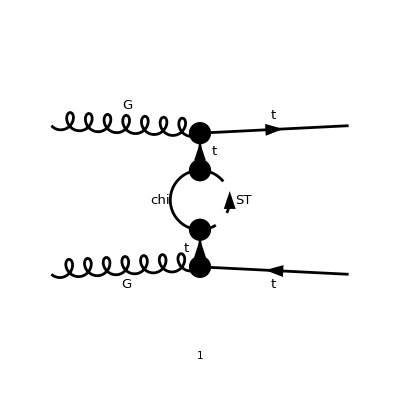

```mathematica
goodDiags=DiagramExtract[allDiags,{56}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{pm,pn},LorentzIndexNames->{μ,ν},OutgoingMomenta->{k1,-p+pn},LoopMomenta->{-q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0}
```

in total: 1 Particles amplitude

-((ⅈ gs γ^μ.(γ̄)^6 T_c2Col5^cc3+ⅈ gs γ^μ.(γ̄)^7 T_c2Col5^cc3).(MT+γ·p).(-ⅈ yDM (γ̄)^7).(mChi+γ·q).(-ⅈ yDM (γ̄)^6).(MT+γ·p).(ⅈ gs γ^ν.(γ̄)^6 T_Col5c1^cc4+ⅈ gs γ^ν.(γ̄)^7 T_Col5c1^cc4))/((p^2-MT^2)^2 (q^2-mChi^2).((p-q)^2-mST^2))

```mathematica
(* Select only leading order *)
ampB=FullSimplify[DiracSimplify[SUNSimplify[ampA/.{deltaCTL->0,deltaCTR->0}],DiracOrder->False]]
```

-(gs^2 yDM^2 (T^cc3 T^cc4)_c2c1 (MT (MT γ^μ.(γ·q).γ^ν.(γ̄)^7+γ^μ.(γ·p).(γ·q).γ^ν.(γ̄)^7+γ^μ.(γ·q).(γ·p).γ^ν.(γ̄)^6)+2 (p·q) γ^μ.(γ·p).γ^ν.(γ̄)^6-p^2 γ^μ.(γ·q).γ^ν.(γ̄)^6))/((p^2-MT^2)^2 (q^2-mChi^2).((p-q)^2-mST^2))

```mathematica
ampCc=FullSimplify[DiracSimplify[FeynAmpDenominatorExplicit[ampC]/.{b0->(a0C-a0T-2Pair[Momentum[p,D],Momentum[p,D]] b1)/(Pair[Momentum[p,D],Momentum[p,D]]+mChi^2+mST^2)},DiracSubstitute67->True]]
```

(ⅈ π^2 gs^2 yDM^2 T_Col5c1^cc4 T_c2Col5^cc3 (mST^2 (a0C-a0T)+b1 p^2 (mChi^2-mST^2+p^2)) ((p^2-MT^2) γ^μ.(γ·p).γ^ν.(γ̄)^5+(MT^2+p^2) γ^μ.(γ·p).γ^ν+2 MT p^2 γ^μ.γ^ν))/(2 p^2 (MT^2-p^2)^2 (mChi^2+mST^2+p^2))

```mathematica
ampC =( TID[SUNSimplify[DiracSimplify[ampB]],q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])
```

1/(((k2-pn)^2-MT^2)^2)ⅈ gs^2 π^2 yDM^2 B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (γ^μ.(γ·k2).γ^ν.(γ̄)^7 MT^2-γ^μ.(γ·pn).γ^ν.(γ̄)^7 MT^2-γ^μ.(γ·k2).(γ·k2).γ^ν.(γ̄)^6 MT-γ^μ.(γ·k2).(γ·k2).γ^ν.(γ̄)^7 MT+γ^μ.(γ·k2).(γ·pn).γ^ν.(γ̄)^6 MT+γ^μ.(γ·k2).(γ·pn).γ^ν.(γ̄)^7 MT+γ^μ.(γ·pn).(γ·k2).γ^ν.(γ̄)^6 MT+γ^μ.(γ·pn).(γ·k2).γ^ν.(γ̄)^7 MT-γ^μ.(γ·pn).(γ·pn).γ^ν.(γ̄)^6 MT-γ^μ.(γ·pn).(γ·pn).γ^ν.(γ̄)^7 MT+γ^μ.(γ·k2).γ^ν.(γ̄)^6 k2^2-γ^μ.(γ·pn).γ^ν.(γ̄)^6 k2^2-2 γ^μ.(γ·k2).γ^ν.(γ̄)^6 (k2·pn)+2 γ^μ.(γ·pn).γ^ν.(γ̄)^6 (k2·pn)+γ^μ.(γ·k2).γ^ν.(γ̄)^6 pn^2-γ^μ.(γ·pn).γ^ν.(γ̄)^6 pn^2) (T^cc3 T^cc4)_c2c1-1/(((k1-pn)^2-MT^2)^2)ⅈ gs^2 π^2 yDM^2 B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (γ^ν.(γ·k1).γ^μ.(γ̄)^7 MT^2-γ^ν.(γ·pn).γ^μ.(γ̄)^7 MT^2+γ^ν.(γ·k1).(γ·k1).γ^μ.(γ̄)^6 MT+γ^ν.(γ·k1).(γ·k1).γ^μ.(γ̄)^7 MT-γ^ν.(γ·k1).(γ·pn).γ^μ.(γ̄)^6 MT-γ^ν.(γ·k1).(γ·pn).γ^μ.(γ̄)^7 MT-γ^ν.(γ·pn).(γ·k1).γ^μ.(γ̄)^6 MT-γ^ν.(γ·pn).(γ·k1).γ^μ.(γ̄)^7 MT+γ^ν.(γ·pn).(γ·pn).γ^μ.(γ̄)^6 MT+γ^ν.(γ·pn).(γ·pn).γ^μ.(γ̄)^7 MT+γ^ν.(γ·k1).γ^μ.(γ̄)^6 k1^2-γ^ν.(γ·pn).γ^μ.(γ̄)^6 k1^2-2 γ^ν.(γ·k1).γ^μ.(γ̄)^6 (k1·pn)+2 γ^ν.(γ·pn).γ^μ.(γ̄)^6 (k1·pn)+γ^ν.(γ·k1).γ^μ.(γ̄)^6 pn^2-γ^ν.(γ·pn).γ^μ.(γ̄)^6 pn^2) (T^cc4 T^cc3)_c2c1-ⅈ gs^2 π^2 ((MT^2 γ^μ.(-(γ·(k2-pn))).γ^ν.(γ̄)^7 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(MT^2 γ^ν.(-(γ·(k1-pn))).γ^μ.(γ̄)^7 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(MT γ^μ.(γ·k2).(-(γ·(k2-pn))).γ^ν.(γ̄)^7 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(MT γ^μ.(-(γ·(k2-pn))).(γ·k2).γ^ν.(γ̄)^6 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(MT γ^μ.(-(γ·(k2-pn))).(γ·pn).γ^ν.(γ̄)^6 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(MT γ^μ.(γ·pn).(-(γ·(k2-pn))).γ^ν.(γ̄)^7 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(MT γ^ν.(γ·k1).(-(γ·(k1-pn))).γ^μ.(γ̄)^7 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(MT γ^ν.(-(γ·(k1-pn))).(γ·k1).γ^μ.(γ̄)^6 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(MT γ^ν.(-(γ·(k1-pn))).(γ·pn).γ^μ.(γ̄)^6 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(MT γ^ν.(γ·pn).(-(γ·(k1-pn))).γ^μ.(γ̄)^7 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(2 γ^μ.(γ·k2).γ^ν.(γ̄)^6 k2^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(γ^μ.(-(γ·(k2-pn))).γ^ν.(γ̄)^6 k2^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(2 γ^μ.(γ·pn).γ^ν.(γ̄)^6 k2^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(4 γ^μ.(γ·k2).γ^ν.(γ̄)^6 (k2·pn) (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(2 γ^μ.(-(γ·(k2-pn))).γ^ν.(γ̄)^6 (k2·pn) (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(4 γ^μ.(γ·pn).γ^ν.(γ̄)^6 (k2·pn) (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(2 γ^μ.(γ·k2).γ^ν.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)-(γ^μ.(-(γ·(k2-pn))).γ^ν.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(2 γ^μ.(γ·pn).γ^ν.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(A_0(mST^2))/(2 (k2^2-2 (k2·pn)+pn^2))+(B_0(k2^2-2 (k2·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k2^2+2 (k2·pn)-pn^2))/(2 (k2^2-2 (k2·pn)+pn^2))) (T^cc3 T^cc4)_c2c1)/(((k2-pn)^2-MT^2)^2)+(2 γ^ν.(γ·k1).γ^μ.(γ̄)^6 k1^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(γ^ν.(-(γ·(k1-pn))).γ^μ.(γ̄)^6 k1^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(2 γ^ν.(γ·pn).γ^μ.(γ̄)^6 k1^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(4 γ^ν.(γ·k1).γ^μ.(γ̄)^6 (k1·pn) (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(2 γ^ν.(-(γ·(k1-pn))).γ^μ.(γ̄)^6 (k1·pn) (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(4 γ^ν.(γ·pn).γ^μ.(γ̄)^6 (k1·pn) (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(2 γ^ν.(γ·k1).γ^μ.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)+(γ^ν.(-(γ·(k1-pn))).γ^μ.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)-(2 γ^ν.(γ·pn).γ^μ.(γ̄)^6 pn^2 (-(A_0(mChi^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(A_0(mST^2))/(2 (k1^2-2 (k1·pn)+pn^2))+(B_0(k1^2-2 (k1·pn)+pn^2,mChi^2,mST^2) (mChi^2-mST^2-k1^2+2 (k1·pn)-pn^2))/(2 (k1^2-2 (k1·pn)+pn^2))) (T^cc4 T^cc3)_c2c1)/(((k1-pn)^2-MT^2)^2)) yDM^2

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]]
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[]; 
 SetMandelstam[s,t,u,p1,p2,p3,p4,p1sq,p2sq,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]];
```

```mathematica
subs = {DiracGamma[Momentum[p2,D],D].DiracGamma[Momentum[p3,D],D]->-DiracGamma[Momentum[p3,D],D].DiracGamma[Momentum[p2,D],D]+2SPD[p2,p3],DiracGamma[Momentum[p1,D],D].DiracGamma[Momentum[p3,D],D]->-DiracGamma[Momentum[p3,D],D].DiracGamma[Momentum[p1,D],D]+2SPD[p1,p3]};
ampEsimp2=DiracSimplify[ampEsimp2/.subs];
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,PaVe}];
```

```mathematica
Table[{lInts[[i]],PaXEvaluateUV[lInts[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4)]},{i,1,Length[lInts]}]
```

(A_0(mChi^2) | mChi^2/(16 π^4 ε_UV)
A_0(mST^2) | mST^2/(16 π^4 ε_UV)
B_0(t,mChi^2,mST^2) | 1/(16 π^4 ε_UV)
B_0(u,mChi^2,mST^2) | 1/(16 π^4 ε_UV))

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2,PaXImplicitPrefactor->1/(2 Pi)^(4)]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[SUNSimplify[Coefficient[ampEsimp2,deltaSp]] (-1/(32 Pi^4  EpsilonUV))];
FullSimplify[DiracSimplify[FullSimplify[FeynAmpDenominatorExplicit[DiracSimplify[(loopUV+ctUV),DiracSubstitute67->True,DiracOrder->True]]]]]
```

0

## Coefficients for Loop Amplitude

```mathematica
subs2={B0[a_,mChi^2,mST^2]:>(ab[a]+(A0[mST^2]-A0[mChi^2]))/(mST^2-mChi^2-a)};
```

```mathematica
ampEsimp3=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp2/.subs]]/.subs2;
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
```

{(γ̄)^6,γ^μ,γ^ν,γ·p1,γ·p2,γ·p4,γ^μ.γ^ν,γ^ν.γ^μ,γ^μ.(γ·p1).γ^ν,γ^μ.(γ·p4).γ^ν,γ^ν.(γ·p2).γ^μ,γ^ν.(γ·p4).γ^μ,γ^μ.(γ·p1).γ^ν.(γ̄)^6,γ^μ.(γ·p1).(γ·p4).γ^ν,γ^μ.(γ·p4).γ^ν.(γ̄)^6,γ^μ.(γ·p4).(γ·p1).γ^ν,γ^ν.(γ·p2).γ^μ.(γ̄)^6,γ^ν.(γ·p2).(γ·p4).γ^μ,γ^ν.(γ·p4).γ^μ.(γ̄)^6,γ^ν.(γ·p4).(γ·p2).γ^μ}

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

### Coefficients for each term

Define shortnames for each coefficient

```mathematica
subs3={(-(MT (-ab[a_] + 2 deltaS MT + 2 deltaSp a_))/(2 (MT^2-a_)^2)):> ab1[s,a],
(2 a_ ( 2 deltaS  MT^2 - deltaS a_ + deltaSp MT^3) - MT^3 ab[a_])/(2 MT a_ (MT^2-a_)^2):> ab2[s,a],
(2 a_ (  deltaS  +deltaSp MT) - MT ab[a_])/(2 MT a_ (MT^2-a_)):> ab3[s,a],
-(-(MT (-ab[a_] + 2 deltaS MT + 2 deltaSp a_))/(2 (MT^2-a_)^2)):> -ab1[s,a],
((MT^3 ab[a_]+2 a_ (deltaS a_ -MT^2( 2 deltaS +  deltaSp MT)))/(2 MT a_ (MT^2-a_)^2)):> -ab2[s,a],
-((2 a_ (  deltaS  +deltaSp MT) - MT ab[a_])/(2 MT a_ (MT^2-a_))):> -ab3[s,a]
};
```

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs^2 yDM^2),{MT,t,u},FullSimplify]/.subs3;
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]],{i,1,Length[su3Terms]}]; 
Simplify[ampTot-ampEsimp3]
```

1/(2 MT t u (MT^2-t)^2 (MT^2-u)^2)ⅈ π^2 gs^2 yDM^2 ((MT^2-u) (u (MT^2-u) (T^cc4 T^cc3)_c2c1 ((MT^2-t) (γ^ν.(γ·p2).γ^μ.(γ̄)^6+γ^ν.(γ·p4).γ^μ.(γ̄)^6) (2 t ((MT t-MT^3) ab3(s,t)+deltaS+deltaSp MT)-MT ab(t))+γ^ν.(γ·p2).γ^μ (2 t (MT (MT^2-t)^2 ab2(s,t)-2 deltaS MT^2+deltaS t-deltaSp MT^3)+MT^3 ab(t))+γ^ν.(γ·p4).γ^μ (2 t (MT (MT^2-t)^2 ab2(s,t)-2 deltaS MT^2+deltaS t-deltaSp MT^3)+MT^3 ab(t)))+t (MT^2-t)^2 (T^cc3 T^cc4)_c2c1 γ^μ.(γ·p1).γ^ν.(γ̄)^6 (MT ab(u)-2 u ((MT u-MT^3) ab3(s,u)+deltaS+deltaSp MT))+t (MT^2-t)^2 (T^cc3 T^cc4)_c2c1 γ^μ.(γ·p4).γ^ν.(γ̄)^6 (MT ab(u)-2 u ((MT u-MT^3) ab3(s,u)+deltaS+deltaSp MT)))-t (MT^2-t)^2 (T^cc3 T^cc4)_c2c1 γ^μ.(γ·p1).γ^ν (2 u (MT (MT^2-u)^2 ab2(s,u)-2 deltaS MT^2+deltaS u-deltaSp MT^3)+MT^3 ab(u))-t (MT^2-t)^2 (T^cc3 T^cc4)_c2c1 γ^μ.(γ·p4).γ^ν (2 u (MT (MT^2-u)^2 ab2(s,u)-2 deltaS MT^2+deltaS u-deltaSp MT^3)+MT^3 ab(u)))

```mathematica
su3Terms
```

((T^cc3 T^cc4)_c2c1 | γ^μ.γ^ν | -(MT (8 deltaSp (p1·p4)^2+p1^2 (-ab(2 (p1·p4)+p1^2+p4^2)+2 deltaS MT+8 deltaSp (p1·p4)+4 deltaSp p4^2)+p4^2 (-ab(2 (p1·p4)+p1^2+p4^2)+2 deltaS MT+2 deltaSp p4^2)+4 (p1·p4) (deltaS MT+2 deltaSp p4^2)+2 deltaSp p1^4))/(2 (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2)^2)
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p1).γ^ν | (MT^3 ab(2 (p1·p4)+p1^2+p4^2)+2 (2 (p1·p4)+p1^2+p4^2) (deltaS (2 (p1·p4)+p1^2+p4^2)-MT^2 (2 deltaS+deltaSp MT)))/(2 MT (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2)^2)
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p4).γ^ν | (MT^3 ab(2 (p1·p4)+p1^2+p4^2)+2 (2 (p1·p4)+p1^2+p4^2) (deltaS (2 (p1·p4)+p1^2+p4^2)-MT^2 (2 deltaS+deltaSp MT)))/(2 MT (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2)^2)
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p1).γ^ν.(γ̄)^6 | -(2 (deltaS+deltaSp MT) (2 (p1·p4)+p1^2+p4^2)-MT ab(2 (p1·p4)+p1^2+p4^2))/(2 MT (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2))
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p1).(γ·p4).γ^ν | (MT ab(2 (p1·p4)+p1^2+p4^2))/(2 (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2)^2)
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p4).γ^ν.(γ̄)^6 | -(2 (deltaS+deltaSp MT) (2 (p1·p4)+p1^2+p4^2)-MT ab(2 (p1·p4)+p1^2+p4^2))/(2 MT (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2))
(T^cc3 T^cc4)_c2c1 | γ^μ.(γ·p4).(γ·p1).γ^ν | (MT ab(2 (p1·p4)+p1^2+p4^2))/(2 (2 (p1·p4)+p1^2+p4^2) (-MT^2+2 (p1·p4)+p1^2+p4^2)^2)
(T^cc4 T^cc3)_c2c1 | γ^ν.γ^μ | -(MT (8 deltaSp (p2·p4)^2+p2^2 (-ab(2 (p2·p4)+p2^2+p4^2)+2 deltaS MT+8 deltaSp (p2·p4)+4 deltaSp p4^2)+p4^2 (-ab(2 (p2·p4)+p2^2+p4^2)+2 deltaS MT+2 deltaSp p4^2)+4 (p2·p4) (deltaS MT+2 deltaSp p4^2)+2 deltaSp p2^4))/(2 (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2)^2)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p2).γ^μ | -(MT^3 ab(2 (p2·p4)+p2^2+p4^2)+2 (2 (p2·p4)+p2^2+p4^2) (deltaS (2 (p2·p4)+p2^2+p4^2)-MT^2 (2 deltaS+deltaSp MT)))/(2 MT (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2)^2)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p4).γ^μ | -(MT^3 ab(2 (p2·p4)+p2^2+p4^2)+2 (2 (p2·p4)+p2^2+p4^2) (deltaS (2 (p2·p4)+p2^2+p4^2)-MT^2 (2 deltaS+deltaSp MT)))/(2 MT (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2)^2)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p2).γ^μ.(γ̄)^6 | (2 (deltaS+deltaSp MT) (2 (p2·p4)+p2^2+p4^2)-MT ab(2 (p2·p4)+p2^2+p4^2))/(2 MT (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2))
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p2).(γ·p4).γ^μ | (MT ab(2 (p2·p4)+p2^2+p4^2))/(2 (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2)^2)
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p4).γ^μ.(γ̄)^6 | (2 (deltaS+deltaSp MT) (2 (p2·p4)+p2^2+p4^2)-MT ab(2 (p2·p4)+p2^2+p4^2))/(2 MT (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2))
(T^cc4 T^cc3)_c2c1 | γ^ν.(γ·p4).(γ·p2).γ^μ | (MT ab(2 (p2·p4)+p2^2+p4^2))/(2 (2 (p2·p4)+p2^2+p4^2) (-MT^2+2 (p2·p4)+p2^2+p4^2)^2))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3), p4(ν)=P(*,4) ] (all momenta are incoming)
 c1 = Anti-Top color = “1”, c2 = Top color = “2”, c3 = Gluon color = “3”, c4 = Gluon color = “4”
spins = [2, 2, 3], 
structure = ‘ P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)’)

s = (p1+p2)^2 =  P(-1,1)**2 + P(-1,2)**2 + 2*P(-1,1)*P(-1,2)
t = (p1+p3)^2  = P(-1,1)**2 + P(-1,3)**2 + 2*P(-1,1)*P(-1,3)
u = (p1+p4)^2  = (p2+p3)^2 = P(-1,2)**2 + P(-1,3)**2 + 2*P(-1,2)*P(-1,3) 
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
```

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

{γ^μ.γ^ν,γ^μ.(γ·p1).γ^ν,γ^μ.(γ·p4).γ^ν,γ^μ.(γ·p1).γ^ν.(γ̄)^6,γ^μ.(γ·p1).(γ·p4).γ^ν,γ^μ.(γ·p4).γ^ν.(γ̄)^6,γ^μ.(γ·p4).(γ·p1).γ^ν,γ^ν.γ^μ,γ^ν.(γ·p2).γ^μ,γ^ν.(γ·p4).γ^μ,γ^ν.(γ·p2).γ^μ.(γ̄)^6,γ^ν.(γ·p2).(γ·p4).γ^μ,γ^ν.(γ·p4).γ^μ.(γ̄)^6,γ^ν.(γ·p4).(γ·p2).γ^μ}

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3],SUNIndex[cc4]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[cc4],SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]->  "T(4,2,-1)*T(3,-1,1)"};
```

```mathematica
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[LorentzIndex[ν,D],D]-> "Gamma(3,2,-1)*Gamma(4,-1,1)",
				   DiracGamma[LorentzIndex[ν,D],D].DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(4,2,-1)*Gamma(3,-1,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[ν, D], D]->  "Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,1)",DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[μ, D], D]->  "Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p1, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p3, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[μ, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[ν, D], D]. DiracGamma[6]->  "Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1)",
DiracGamma[LorentzIndex[ν, D], D] . DiracGamma[Momentum[p2, D], D] . DiracGamma[LorentzIndex[μ, D], D]. DiracGamma[6]->  "Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1)"};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
```

{γ^μ.(γ·p1).γ^ν.(γ̄)^6→Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1),γ^μ.(γ·p2).γ^ν.(γ̄)^6→Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1),γ^μ.(γ·p3).γ^ν.(γ̄)^6→Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1),γ^ν.(γ·p1).γ^μ.(γ̄)^6→Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1),γ^ν.(γ·p2).γ^μ.(γ̄)^6→Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1),γ^ν.(γ·p3).γ^μ.(γ̄)^6→Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1),γ^μ.(γ·p1).γ^ν→Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,1),γ^μ.(γ·p2).γ^ν→Gamma(3,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(4,-3,1),γ^μ.(γ·p3).γ^ν→Gamma(3,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(4,-3,1),γ^ν.(γ·p1).γ^μ→Gamma(4,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(3,-3,1),γ^ν.(γ·p2).γ^μ→Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,1),γ^ν.(γ·p3).γ^μ→Gamma(4,2,-1)*P(-2,3)*Gamma(-2,-1,-3)*Gamma(3,-3,1),γ^μ.γ^ν→Gamma(3,2,-1)*Gamma(4,-1,1),γ^ν.γ^μ→Gamma(4,2,-1)*Gamma(3,-1,1)}

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=20;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*(",fullStr,")"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,-1)*T(4,-1,1)

FFVVNP21

( Gamma(3,2,-1)*Gamma(4,-1,1) )*((-0.5*(MT*(2*deltaSp*Pair(Momentum(p1,D),Momentum(p1,D))**2 + 8*deltaSp*Pair(Momentum(p1,D),Momentum(p4,D))**2 + 4*Pair(Momentum(p1,D),Momentum(p4,D))*(deltaS*MT + 2*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D))) + Pair(Momentum(p4,D),Momentum(p4,D))*(2*deltaS*MT - ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D))) + Pair(Momentum(p1,D),Momentum(p1,D))*(2*deltaS*MT - ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 8*deltaSp*Pair(Momentum(p1,D),Momentum(p4,D)) + 4*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D)))))/((Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP22

( Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,1) )*(((MT**3*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(2.*MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP23

StringJoin::string: String expected at position 2 in ( <>«1»<> )*(((MT**3*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Mome…m(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(2.*MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2))).

( <>(γ^μ.(γ·p4).γ^ν)<> )*(((MT**3*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(2.*MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP24

( Gamma(3,2,-1)*P(-2,1)*Gamma(-2,-1,-3)*Gamma(4,-3,-4)*ProjP(-4,1) )*((-0.5*(-(MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))))

FFVVNP25

StringJoin::string: String expected at position 2 in ( <>(γ^μ.(γ·p1).(γ·p4).γ^ν)<> )*(((MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2))).

( <>(γ^μ.(γ·p1).(γ·p4).γ^ν)<> )*(((MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP26

StringJoin::string: String expected at position 2 in ( <>(γ^μ.(γ·p4).γ^ν.(γ̄)^6)<> )*((-0.5*(-(MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

( <>(γ^μ.(γ·p4).γ^ν.(γ̄)^6)<> )*((-0.5*(-(MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))))

FFVVNP27

( <>(γ^μ.(γ·p4).(γ·p1).γ^ν)<> )*(((MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

------------------

T(4,2,-1)*T(3,-1,1)

FFVVNP28

( Gamma(4,2,-1)*Gamma(3,-1,1) )*((-0.5*(MT*(2*deltaSp*Pair(Momentum(p2,D),Momentum(p2,D))**2 + 8*deltaSp*Pair(Momentum(p2,D),Momentum(p4,D))**2 + 4*Pair(Momentum(p2,D),Momentum(p4,D))*(deltaS*MT + 2*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D))) + Pair(Momentum(p4,D),Momentum(p4,D))*(2*deltaS*MT - ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D))) + Pair(Momentum(p2,D),Momentum(p2,D))*(2*deltaS*MT - ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 8*deltaSp*Pair(Momentum(p2,D),Momentum(p4,D)) + 4*deltaSp*Pair(Momentum(p4,D),Momentum(p4,D)))))/((Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP29

( Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,1) )*((-0.5*(MT**3*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(MT*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP30

( <>(γ^ν.(γ·p4).γ^μ)<> )*((-0.5*(MT**3*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(MT*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP31

( Gamma(4,2,-1)*P(-2,2)*Gamma(-2,-1,-3)*Gamma(3,-3,-4)*ProjP(-4,1) )*(((-(MT*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*MT*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))))

FFVVNP32

( <>(γ^ν.(γ·p2).(γ·p4).γ^μ)<> )*(((MT*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

FFVVNP33

( <>(γ^ν.(γ·p4).γ^μ.(γ̄)^6)<> )*(((-(MT*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*MT*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))))

FFVVNP34

( <>(γ^ν.(γ·p4).(γ·p2).γ^μ)<> )*(((MT*ab(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p2,D),Momentum(p2,D)) + 2*Pair(Momentum(p2,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2)))

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpSelf.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=20;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
If[Length[terms1]==0,Continue[]];
vertexCounter += 1;
Write[outF,StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=StringJoin["(",ToString[FortranForm[terms1[[1,3]]]],")"];
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr,")"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

OpenWrite::noopen: Cannot open ../../Models/Top-FormFactorsOneLoop-UFO/lffvvnpSelf.txt.

Write::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of Write::strml will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in ( <>«1»<> )*( ((MT**3*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))) + 2*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-(MT**2*(2*deltaS + deltaSp*MT)) + deltaS*(Pair(Mom…m(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))/(2.*MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2))).

StringJoin::string: String expected at position 2 in ( <>(γ^μ.(γ·p1).(γ·p4).γ^ν)<> )*( ((MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(2.*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))**2))).

StringJoin::string: String expected at position 2 in ( <>(γ^μ.(γ·p4).γ^ν.(γ̄)^6)<> )*( (-0.5*(-(MT*ab(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))) + 2*(deltaS + deltaSp*MT)*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D))))/(MT*(Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))*(-MT**2 + Pair(Momentum(p1,D),Momentum(p1,D)) + 2*Pair(Momentum(p1,D),Momentum(p4,D)) + Pair(Momentum(p4,D),Momentum(p4,D)))))).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[$Failed]